```mathematica
f=η-10n/(1+n^2);(*\tilde{f}*)
source=p-n;
fTot={f,0,source};(*adopt for source terms in u or v*)
```

```mathematica
fixedParams={Du->1,p->20,L->100}
```

{Du→1,p→20,L→100}

### Fixed point

```mathematica
fp=First@Solve[Thread[{f,-f}+eps fTot[[2;;]]==0]/.{n->(u+v),η->(v+Du/Dv u)},{u,v}]
```

{u→(9 Dv p-Dv p^3)/((Du-Dv) (1+p^2)),v→(p (Du-10 Dv+Du p^2))/((Du-Dv) (1+p^2))}

### Linear stability

```mathematica
jac=(DiagonalMatrix[{-Du q2,-Dv q2}]+D[({f,-f}+eps fTot[[2;;]])/.{n->(u+v),η->(v+Du/Dv u)},{{u,v}}])/.fp;
jac//MatrixForm
```

(Du/Dv+(20 ((p (Du-10 Dv+Du p^2))/((Du-Dv) (1+p^2))+(9 Dv p-Dv p^3)/((Du-Dv) (1+p^2)))^2)/((1+((p (Du-10 Dv+Du p^2))/((Du-Dv) (1+p^2))+(9 Dv p-Dv p^3)/((Du-Dv) (1+p^2)))^2)^2)-10/(1+((p (Du-10 Dv+Du p^2))/((Du-Dv) (1+p^2))+(9 Dv p-Dv p^3)/((Du-Dv) (1+p^2)))^2)-Du q2 | 1+(20 ((p (Du-10 Dv+Du p^2))/((Du-Dv) (1+p^2))+(9 Dv p-Dv p^3)/((Du-Dv) (1+p^2)))^2)/((1+((p (Du-10 Dv+Du p^2))/((Du-Dv) (1+p^2))+(9 Dv p-Dv p^3)/((Du-Dv) (1+p^2)))^2)^2)-10/(1+((p (Du-10 Dv+Du p^2))/((Du-Dv) (1+p^2))+(9 Dv p-Dv p^3)/((Du-Dv) (1+p^2)))^2)
-Du/Dv-eps-(20 ((p (Du-10 Dv+Du p^2))/((Du-Dv) (1+p^2))+(9 Dv p-Dv p^3)/((Du-Dv) (1+p^2)))^2)/((1+((p (Du-10 Dv+Du p^2))/((Du-Dv) (1+p^2))+(9 Dv p-Dv p^3)/((Du-Dv) (1+p^2)))^2)^2)+10/(1+((p (Du-10 Dv+Du p^2))/((Du-Dv) (1+p^2))+(9 Dv p-Dv p^3)/((Du-Dv) (1+p^2)))^2) | -1-eps-(20 ((p (Du-10 Dv+Du p^2))/((Du-Dv) (1+p^2))+(9 Dv p-Dv p^3)/((Du-Dv) (1+p^2)))^2)/((1+((p (Du-10 Dv+Du p^2))/((Du-Dv) (1+p^2))+(9 Dv p-Dv p^3)/((Du-Dv) (1+p^2)))^2)^2)+10/(1+((p (Du-10 Dv+Du p^2))/((Du-Dv) (1+p^2))+(9 Dv p-Dv p^3)/((Du-Dv) (1+p^2)))^2)-Dv q2)

Find the edges of the band of unstable modes:

```mathematica
unstableBand=q2/.Solve[Eigenvalues[jac][[2]]==0,q2];
```

### Stability threshold on infinite domain

Find onset where unstable band emerges.

```mathematica
epsC=Assuming[{unstableBand[[1]]>0,unstableBand[[2]]>0,eps>0},eps/.Solve[Evaluate[unstableBand[[1]]==unstableBand[[2]]],eps]];
```

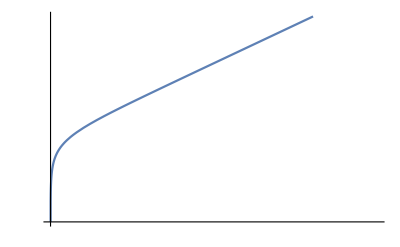

```mathematica
LogLogPlot[Evaluate[epsC/.fixedParams],{Dv,1,10^6},
PlotRange->{10^-7,10},
Ticks->{{{1,},{10^6,}},{{10^-7,},{10^0,}}}]
```